# ChristopherWolfram/ForeignFunctionInterface

Efficiently connect to C-compatible libraries

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ForeignFunctionInterface.nb"DocumentationEnglishGuidesForeignFunctionInterface.nb

"ReferencePages"

"Symbols"

"BufferToList.nb"DocumentationEnglishReferencePagesSymbolsBufferToList.nb

"BufferToNumericArray.nb"DocumentationEnglishReferencePagesSymbolsBufferToNumericArray.nb

"BufferToString.nb"DocumentationEnglishReferencePagesSymbolsBufferToString.nb

"CallForeignFunction.nb"DocumentationEnglishReferencePagesSymbolsCallForeignFunction.nb

"CreateBuffer.nb"DocumentationEnglishReferencePagesSymbolsCreateBuffer.nb

"CreateCallback.nb"DocumentationEnglishReferencePagesSymbolsCreateCallback.nb

"CreateForeignFunction.nb"DocumentationEnglishReferencePagesSymbolsCreateForeignFunction.nb

"CreateManagedExpression.nb"DocumentationEnglishReferencePagesSymbolsCreateManagedExpression.nb

"DeleteBuffer.nb"DocumentationEnglishReferencePagesSymbolsDeleteBuffer.nb

"DeleteCallback.nb"DocumentationEnglishReferencePagesSymbolsDeleteCallback.nb

"DereferenceBuffer.nb"DocumentationEnglishReferencePagesSymbolsDereferenceBuffer.nb

"GetManagedExpression.nb"DocumentationEnglishReferencePagesSymbolsGetManagedExpression.nb

"ListToBuffer.nb"DocumentationEnglishReferencePagesSymbolsListToBuffer.nb

"NumericArrayToBuffer.nb"DocumentationEnglishReferencePagesSymbolsNumericArrayToBuffer.nb

"OpaqueRawPointer.nb"DocumentationEnglishReferencePagesSymbolsOpaqueRawPointer.nb

"PopulateBuffer.nb"DocumentationEnglishReferencePagesSymbolsPopulateBuffer.nb

"StringToBuffer.nb"DocumentationEnglishReferencePagesSymbolsStringToBuffer.nb

"Tutorials"

"CreatingALinkToSQLite.nb"DocumentationEnglishTutorialsCreatingALinkToSQLite.nb

"FFITypes.nb"DocumentationEnglishTutorialsFFITypes.nb

"Kernel"

"Buffer.wl"KernelBuffer.wl

"ForeignFunctionInterface.wl"KernelForeignFunctionInterface.wl

"LibFFI"

"BaseTypes.wl"KernelLibFFIBaseTypes.wl

"Callback.wl"KernelLibFFICallback.wl

"CallForeignFunction.wl"KernelLibFFICallForeignFunction.wl

"Constants.wl"KernelLibFFIConstants.wl

"CreateForeignFunction.wl"KernelLibFFICreateForeignFunction.wl

"ExpressionConversion.wl"KernelLibFFIExpressionConversion.wl

"FFIType.wl"KernelLibFFIFFIType.wl

"LibFFI.wl"KernelLibFFILibFFI.wl

"RawFunctionLoading.wl"KernelLibFFIRawFunctionLoading.wl

"ManagedExpression.wl"KernelManagedExpression.wl

"OpaqueRawPointer.wl"KernelOpaqueRawPointer.wl

"LibraryResources"

"Linux-x86-64"

"ffiConstants.so"LibraryResourcesLinux-x86-64ffiConstants.so

"ForeignFunctionInterface.so"LibraryResourcesLinux-x86-64ForeignFunctionInterface.so

"libffi.a"LibraryResourcesLinux-x86-64libffi.a

"libffi.la"LibraryResourcesLinux-x86-64libffi.la

"libffi.so"LibraryResourcesLinux-x86-64libffi.so

"libffi.so.8"LibraryResourcesLinux-x86-64libffi.so.8

"libffi.so.8.1.2"LibraryResourcesLinux-x86-64libffi.so.8.1.2

"MacOSX-x86-64"

"ffiConstants.dylib"LibraryResourcesMacOSX-x86-64ffiConstants.dylib

"ForeignFunctionInterface.dylib"LibraryResourcesMacOSX-x86-64ForeignFunctionInterface.dylib

"libffi.8.dylib"LibraryResourcesMacOSX-x86-64libffi.8.dylib

"libffi.a"LibraryResourcesMacOSX-x86-64libffi.a

"libffi.dylib"LibraryResourcesMacOSX-x86-64libffi.dylib

"libffi.la"LibraryResourcesMacOSX-x86-64libffi.la

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

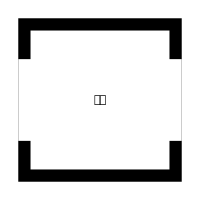

```mathematica
Graphics[{
{Black,Rectangle[{-1,-1},{1,1}],
White,Rectangle[{-0.85,-0.85},{0.85,0.85}],
Rectangle[{-1,-0.5},{1,0.5}]
},
{FontSize->Scaled[0.35],Text["𒅴𒁇"]}
},PlotRange->1,PlotRangePadding->0]
```

### Basic Description

ForeignFunctionInterface makes it possible to efficiently call functions from C-compatible libraries directly from the Wolfram Language, without the need to compile an interface layer.

### Details

This paclet uses libffi to dynamically link to C-compatible libraries at runtime

Though this paclet could be built on all platforms supported by Wolfram Language, it is currently only built for x86 macOS and Linux.

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["ChristopherWolfram`ForeignFunctionInterface`"];
```

### Basic Examples

Load a library:

```mathematica
LibraryLoad["compilerDemoBase"];
```

Create a ForeignFunctionObject referring to a function from the library:

```mathematica
addone=CreateForeignFunction["addone",{"CInt"}->"CInt"]
```

DataStructure[ForeignFunctionObject, $Failed]

Call the foreign function:

```mathematica
CallForeignFunction[addone,{12}]
```

13

### Scope

Function calls have very little overhead:

```mathematica
LibraryLoad["compilerDemoBase"];
addone=CreateForeignFunction["addone",{"CInt"}->"CInt"];
```

```mathematica
RepeatedTiming@CallForeignFunction[addone,{12}]
```

{2.69192×10^-7,13}

### Applications

Create a foreign function for the RAND_bytes function from OpenSSL:

```mathematica
randBytes=CreateForeignFunction["RAND_bytes",{"OpaqueRawPointer","CInt"}->"CInt"]
```

DataStructure[ForeignFunctionObject, $Failed]

Create a memory-managed buffer into which the random bytes can be written:

```mathematica
out=CreateManagedExpression[CreateBuffer["UnsignedInteger8",32],DeleteBuffer]
```

DataStructure[ManagedExpression, $Failed]

Generate the random bytes:

```mathematica
CallForeignFunction[randBytes,{out,32}]
```

1

Read the output:

```mathematica
Normal@BufferToNumericArray[out,"UnsignedInteger8",32]
```

{142,68,254,3,106,220,152,190,225,67,96,246,51,224,241,144,66,67,187,126,74,237,241,103,225,39,167,143,161,229,63,206}

Package into a function:

```mathematica
generateRandomBytes[len_]:=
Module[{out=CreateManagedExpression[CreateBuffer["UnsignedInteger8",len],DeleteBuffer]},
CallForeignFunction[randBytes,{out,len}];
BufferToNumericArray[out,"UnsignedInteger8",len]
]
```

```mathematica
Normal@generateRandomBytes[128]
```

{54,251,198,119,194,40,96,223,62,95,181,100,241,150,58,164,0,97,238,27,40,28,202,115,226,100,245,180,109,97,10,200,183,157,209,53,50,185,180,33,151,133,25,15,224,213,211,20,152,230,245,27,182,241,135,110,11,153,220,86,20,166,155,27,202,138,100,93,19,164,230,55,165,111,101,124,182,214,239,240,162,183,179,27,222,166,175,152,238,253,78,19,194,4,127,109,18,99,162,150,247,85,200,122,131,45,62,216,55,44,72,88,29,3,112,232,152,35,171,203,209,49,15,66,120,178,195,189}

The foreign function is very efficient:

```mathematica
RepeatedTiming[generateRandomBytes[10000000];]
```

{0.00558877,Null}

```mathematica
RepeatedTiming[RandomInteger[{0,255},10000000];]
```

{0.0278601,Null}

Create a foreign function for the SHA256 function from OpenSSL:

```mathematica
sha256=CreateForeignFunction["SHA256",
{"OpaqueRawPointer","CUnsignedLong","OpaqueRawPointer"}->"OpaqueRawPointer"
]
```

DataStructure[ForeignFunctionObject, $Failed]

Create a buffer containing the plaintext to hash:

```mathematica
plaintext="Hello, World!";
plaintextBuffer=CreateManagedExpression[StringToBuffer[plaintext],DeleteBuffer]
```

DataStructure[ManagedExpression, $Failed]

Create a buffer into which to write the hash:

```mathematica
ciphertext=CreateManagedExpression[CreateBuffer["UnsignedInteger8",32],DeleteBuffer]
```

DataStructure[ManagedExpression, $Failed]

Generate inputs and execute the hash:

```mathematica
CallForeignFunction[sha256,{
plaintextBuffer,
StringLength[plaintext],
ciphertext
}]
```

OpaqueRawPointer[…]

Extract the results:

```mathematica
Normal@BufferToNumericArray[ciphertext,"UnsignedInteger8",32]
```

{223,253,96,33,187,43,213,176,175,103,98,144,128,158,195,165,49,145,221,129,199,247,10,75,40,104,138,54,33,130,152,111}

Compare with the built-in function Hash:

```mathematica
Normal@Hash[plaintext,"SHA256","ByteArray"]
```

{223,253,96,33,187,43,213,176,175,103,98,144,128,158,195,165,49,145,221,129,199,247,10,75,40,104,138,54,33,130,152,111}

Package into a function:

```mathematica
generateSHA256[plaintext_]:=
Module[{
plaintextBuffer=CreateManagedExpression[StringToBuffer[plaintext],DeleteBuffer],
ciphertext=CreateManagedExpression[CreateBuffer["UnsignedInteger8",32],DeleteBuffer]
},
CallForeignFunction[sha256,{
plaintextBuffer,
StringLength[plaintext],
ciphertext
}];
BufferToNumericArray[ciphertext,"UnsignedInteger8",32]
]
```

```mathematica
generateSHA256["Hello, World!"]//Normal
```

{223,253,96,33,187,43,213,176,175,103,98,144,128,158,195,165,49,145,221,129,199,247,10,75,40,104,138,54,33,130,152,111}

The packaged function is much faster than the built-in one:

```mathematica
RepeatedTiming@Hash[plaintext,"SHA256","ByteArray"]
```

{0.000427803,ByteArray[…]}

```mathematica
RepeatedTiming@generateSHA256[plaintext]
```

{8.75591×10^-6,NumericArray[…]}

### Properties and Relations

CreateForeignFunction can create callable links to libraries much faster than custom compiling a link:

```mathematica
LibraryLoad["compilerDemoBase"];
```

```mathematica
RepeatedTiming[addone=CreateForeignFunction["addone",{"CInt"}->"CInt"]]
```

{0.000129924,DataStructure[ForeignFunctionObject, $Failed]}

```mathematica
RepeatedTiming[addoneCf=FunctionCompile[
LibraryFunctionDeclaration["addone","compilerDemoBase",{"CInt"}->"CInt"],
Function[Typed[x,"CInt"],LibraryFunction["addone"][x]]
]]
```

{0.273241,CompiledCodeFunction[…]}

However, the custom compiled versions usually have slightly less overhead:

```mathematica
RepeatedTiming[CallForeignFunction[addone,{10}]]
```

{2.87258×10^-7,11}

```mathematica
RepeatedTiming[addoneCf[10]]
```

{1.52347×10^-7,11}

### Possible Issues

Platforms other than x86 Linux and macOS can be made to work by adding builds of libffi and the ffiConstants library (found in the source repository) to LibraryResources. Then, the linking code can be created by building the compiled component in a one-time operation:

```mathematica
BuildCompiledComponent["ForeignFunctionInterface",PacletObject["ChristopherWolfram/ForeignFunctionInterface"]]
```

Success[…]

## Source & Additional Information

### Creator

Christopher Wolfram

### Source Control Repository

https://github.com/chriswolfram/ForeignFunctionInterface

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

FFI

foreign function interface

library

libraries

dynamic libraries

dynamic library

external libraries

external library

C

linking

link

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

libffi homepage

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

There are some know issues with managed expressions. The design of that system will likely have to change. For example, managed expressions stored in a With are often freed before their bodies can be used:

```mathematica
With[{buf=CreateManagedExpression[foo,Echo["freed"]&]},
EchoLabel["func"][GetManagedExpression[buf]]
]
```

freed

func  foo

foo

This is still a work in progress, and there are a few missing features, though they are all relatively simple to implement. Here are some of them:

Windows support. The current platform list is just those that I can easily build for.

More functions for creating and manipulating buffers / structs.

More natural calling syntax.

Perhaps automatic type conversion (so a string could be passed to an argument with type OpaqueRawPointer, etc.)

The logo for this paclet is Sumerian for "foreign language" (or at least an attempt to mean that).